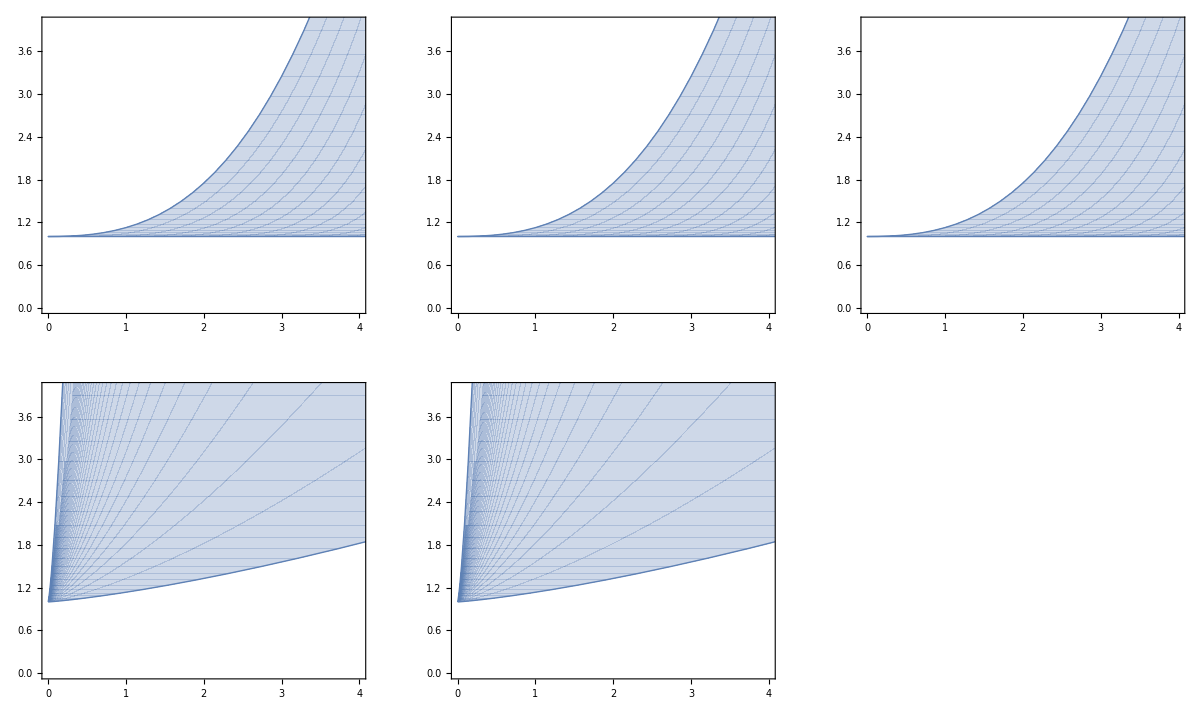

```mathematica
u[s_]:=s^2+4*s^3+1;
x[s_,t_]:=4s+t*s^3-3*s^2*t+4*t;
y[s_,t_]:=4s^2/(5t);
h0=ParametricPlot[{x[s,t],u[s]},{s,0,2},{t,0,5},PlotRange -> {0,4}];
h1=ParametricPlot[{x[s,t],u[s]},{s,0,2},{t,0,5},PlotRange -> {0,4}];
h2=ParametricPlot[{x[s,t],u[s]},{s,0,2},{t,0,5},PlotRange -> {0,4}];
h3=ParametricPlot[{y[s,t],u[s]},{s,0,2},{t,0,3},PlotRange -> {0,4}];
h4=ParametricPlot[{y[s,t],u[s]},{s,0,2},{t,0,3},PlotRange -> {0,4}];
Show[GraphicsArray[{{h0,h1,h2},{h3,h4}}],FrameTicks->None,Frame -> False]
```

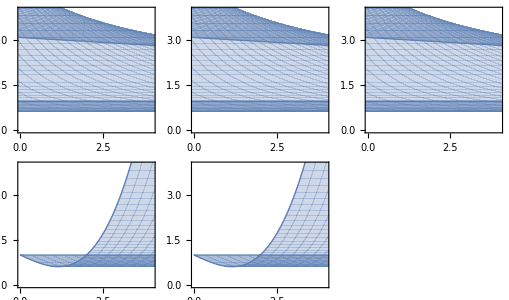

```mathematica
u[s_]:=s^3-s+1;
x[s_,t_]:=4t/s^3-3*s^t+4*t;
y[s_,t_]:=s*2+6t;
h0=ParametricPlot[{x[s,t],u[s]},{s,0,2},{t,0,5},PlotRange -> {0,4}];
h1=ParametricPlot[{x[s,t],u[s]},{s,0,2},{t,0,5},PlotRange -> {0,4}];
h2=ParametricPlot[{x[s,t],u[s]},{s,0,2},{t,0,5},PlotRange -> {0,4}];
h3=ParametricPlot[{y[s,t],u[s]},{s,0,2},{t,0,3},PlotRange -> {0,4}];
h4=ParametricPlot[{y[s,t],u[s]},{s,0,2},{t,0,3},PlotRange -> {0,4}];
Show[GraphicsArray[{{h0,h1,h2},{h3,h4}}],FrameTicks->None,Frame -> False]
```